# Small Vibrations and Simple Harmonic Motion for Two Interacting Ions

Consider the Hamiltonian 

h=M (Ṙ)^2/4 +  m  (u̇)^2/2  + V(|u|)

where R, u  are the ion coordinates defined in Eq. 7.56 of the text. (Here we replaced the symbol μ, for the reduced mass by the symbol m.) The equations of motion are
M R̈/2= 0
 m ü=-(∂V)/(∂u)
In an ion trap, the ions experience a combination of trapping potentials as well as a repulsive Coulomb force. Let’s assume that the effective potential has the form.
V= -1/√((u-a)^2+a^2)
We plot this potential, as a function of ion relative separation (and choosing a=1)

```mathematica
ClearAll["Global`*"]
```

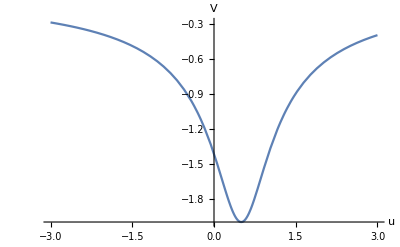

```mathematica
Plot[-1/√((u-a)^2+a^2) /. a->0.5,{u,-3,3},PlotRange->All,AxesLabel->{u,V}]
```

We note that the ions assume an equilibrium position at u=a, with V=-1/|a|. Near that equilibrium position V(u)≈-1/|a| + (u-a)^2/2|a|^3 .

(-a+u)^2/(2 Abs[a]^3)-1/Abs[a]

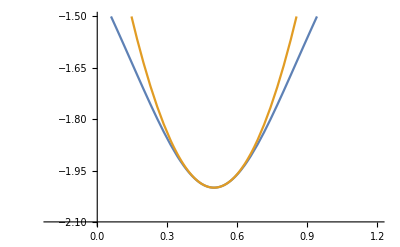

```mathematica
harmonic[u_,a_]=-1/Abs[a]+(u-a)^2/2/Abs[a]^3
Module[{a=0.5},Plot[{-1/√((u-a)^2+a^2),harmonic[u,a],AxesLabel->{u,V}},{u,-0.2,1.2},PlotRange->{-2.1,-1.5}]]
```

In this figure we plotted the potential V(u) (blue line) in the region near its minimum at u=a, and superimposed on it the harmonic approximation to it ( the orange line),.

For small oscillations about the equilibrium position u=a, this describes a SHO with "spring" constant k=1/|a|^3 and, according to our discussion in Section 7.4, it should exhibit SHO motion of frequency

ν =√(k/m) = √(1/(m |a|^3)) 

Using the Lagrange equations, the equation of motion for relative coordinate u(t) becomes

m ü=-(u-a)/(a^2+ (u-a)^2)^(3/2)

```mathematica
(* we initialize the parameters m,a, as well as the initial value x(0), and velocity ẋ(0) *)
m=1;a=0.5;v0=0;u0=a+1/4;ν=Sqrt[1/Abs[a]^3/m];A=Sqrt[(u0-a)^2+v0^2/ν^2];
solu=Flatten[NDSolve[{u''[t]+(u[t]-a)/(m(a^2+(u[t]-a)^2)^(3/2))==0,u[0]==u0,u'[0]==v0},u,{t,0,20 Pi/ν}]];
ufun[t_]=u[t] /. solu
```

InterpolatingFunction[{{0., 22.2144}}, <>][t]

Let’s compare solution for u(t),  given by ufun[t], with the SHO form y(t)=A Sin(ν t + α),  where

y(0)/y'(0)=Tan(α)
A=√(y(0)^2+y'(0)^2/ν^2)

```mathematica
(* Harmonic oscillator approximation *)
sho[t_]=a+ A Sin[ν t + N[ArcTan[(u0-a)/(v0+10^(-12))]]]
```

0.5+0.25 Sin[1.5708+2.82843 t]

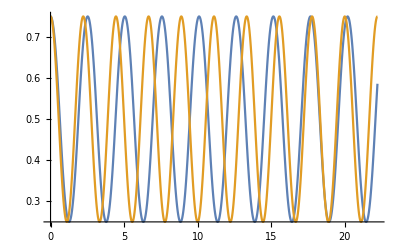

```mathematica
Plot[{ufun[t],sho[t]},{t,0,20Pi/ν }]
```

For small values of t, the harmonic oscillator approximation (blue line) is in harmony with the solution u(t). At larger values of t, the phase  of the latter appears to drift from  the SHO value α.

Now the equation of motion for the CM coordinate is trivial and just leads to the relation

R(t)=vcm t+ R(0)

```mathematica
(* choose initial condition *)
vcm=0.05;
R[t_]=vcm t;
```

Using relations (7.54) in the text we find

```mathematica
Ra[t_]=R[t]+ufun[t]/2;
Rb[t_]=R[t]-ufun[t]/2;
```

With these relations we can simulate the motion of the two ions, as shown below.

```mathematica
g[t_]:=Graphics[{{Red,Disk[{Ra[t],0},0.1]},Disk[{Rb[t],0},0.1]},PlotRange->{{-0.5 ,2},{-0.1,0.1}}]
```

```mathematica
Manipulate[g[t],{t,0,20Pi/ν},SaveDefinitions->True]
```

### Problems.

(1) Explore how the SHO approximation for u(t) fares, for different values of parameter a.

(2)  Eq. (1) predicts that  the center of mass motion is given by  R(t) = Vcm t, where Vcm is a constant velocity. In the Cirac-Zoller model, the internal states of the ion are coupled to the center of mass motion of ions constrained in a trap. We can simulate the latter by replacing the right hand side of
Eq. (1) with a harmonic potential. Explore how the motion illustrated, in the animation above,  is altered in that case.